# Variational strategy for the time-evolution of a local observable

## (see Notes_Thais/Local_op_variational.pdf) - changing the order of K> and K< to be consistent with the optimization process used to determine φ_j(0)

```mathematica
ClearAll["Global`*"]
```

Length of the spin chain:

```mathematica
L=5;
```

Dept of the ansatz (P):

```mathematica
𝒫=1;
```

## Constructing Hamiltonian and S_z (functions from TI’s Mathematica) - compile this entire block

```mathematica
FlipFlop[n_,i_,j_]:=Block[
{v=IntegerDigits[n,2,L]},
If[v[[i]]≠0&&v[[j]]≠1,
v[[i]]=v[[i]]-1;
v[[j]]=v[[j]]+1;
FromDigits[v,2]
,
-1]
]
Raise[n_,i_]:=Block[
{v=IntegerDigits[n,2,L]},
If[v[[Mod[i,L,1]]]≠1,
v[[i]]=v[[i]]+1;
FromDigits[v,2]
,
-1]
]
U[t_,e_,v_]:=Transpose[v].DiagonalMatrix[Exp[-ⅈ e t]].Conjugate[v]
```

```mathematica
Id=IdentityMatrix[2^L];
Heis=Table[
SparseArray[
Flatten@Table[
Block[{h=FlipFlop[j,i,k],v=2IntegerDigits[j,2,L]-1},
If[h≠-1,
{{j+1,h+1}->2.,
{h+1,j+1}->2.,
{j+1,j+1}->N[v[[i]]*v[[k]]]},
{{j+1,j+1}->N[v[[i]]*v[[k]]]}]
]
,{j,0,2^L-1}]
,{2^L,2^L}]
,{i,1,L},{k,1,L}];

Sz=Monitor[Table[
SparseArray[
Table[
Block[{v=2IntegerDigits[j,2,L]-1},
{j+1,j+1}->N[v[[i]]]
]
,{j,0,2^L-1}]
,{2^L,2^L}]
,{i,1,L}],i];
SzTot=Sum[Sz[[i]],{i,L}];

Sp=Monitor[Table[
SparseArray[
DeleteCases[Table[
Block[{h=Raise[j,i]},
If[h≠-1,
{h+1,j+1}->1.]
]
,{j,0,2^L-1}]
,Null]
,{2^L,2^L}]
,{i,1,L}],i];
Sm=Monitor[Table[Transpose[Sp[[i]]]
,{i,1,L}],i];
```

## Testing commutators

```mathematica
Commut[M1_,M2_]:=M1.M2-M2.M1;
```

```mathematica
Length[Heis[[1,2]]]
```

32

```mathematica
vzeros=ConstantArray[0,Length[Heis[[1,2]]]];
Mzeros=DiagonalMatrix[vzeros];
```

```mathematica
Commut[Heis[[2,3]],Heis[[4,5]]]==Mzeros
```

True

```mathematica
{Commut[Heis[[1,2]],Heis[[3,4]]]==Mzeros,Commut[Heis[[1,2]],Heis[[5,1]]]==Mzeros}
```

{True,False}

```mathematica
Commut[Heis[[3,4]],Heis[[5,1]]]==Mzeros
```

True

```mathematica
Simplify[Chop[Commut[MatrixExp[-I*φ5*Heis[[5,1]]],Heis[[1,2]]]]];
```

```mathematica
Commut[Heis[[5,1]],Heis[[1,2]]]//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0.
0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | -4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 4. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

## Ansatz (using parts of TI’s Mathematica)

Initial state is the Nèel state:

```mathematica
c=Table[(1+(-1)^i)/2,{i,L}]
```

{0,1,0,1,0}

```mathematica
(*init=UnitVector[2^L,FromDigits[c,2]]*)
(*Neel state {down,up,down,up,down}*)
init={0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}
(*init={0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}*)
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

Construct vector φ = (θ_(1,1),ϕ_(1,2),θ_(1,3),...,ϕ_(𝒫,1),...)=(φ[1],φ[2],φ[3],...,φ[PL])

```mathematica
(*vecφ[Pdepth_,Lsite_]:=Module[{},
Table[φ[j],{j,1,Pdepth*Lsite}]];*)

(*vecφnum[Pdepth_,Lsite_]:=Module[{},
Table[RandomReal[{0,2*Pi}],{j,1,Pdepth*Lsite}]];*)
```

### Functions:

U_even(ϕ_s) and U_odd(θ_s) for fixed s:

```mathematica
(*anglesvec=(Subscript[θ, s,1],Subscript[ϕ, s,2],Subscript[θ, s,3],...) for a fixed s*)
Us[anglesvec_,Lsite_]:=Module[{φ,n,Meven,Modd,j1,j2},
(*angvecs={Subscript[θ, s,1],Subscript[ϕ, s,2],Subscript[θ, s,3],Subscript[ϕ, s,4],...} for fixed s constructed outside of this function*)
φ=anglesvec;
n=Lsite; (*number of sites of the chain*)
Meven=IdentityMatrix[2^n];
Modd=IdentityMatrix[2^n];
Do[
j1=j;
j2=If[j==n,Mod[j+1,n],j+1];
If[EvenQ[j]==True,Meven=MatrixExp[(-I)*φ[[j]]*Heis[[j1,j2]]].Meven,Modd=MatrixExp[(-I)*φ[[j]]*Heis[[j1,j2]]].Modd]
,{j,1,n}];
{Meven,Modd}
];
```

```mathematica
(*anglesvec here is the complete (Subscript[θ, s,1],Subscript[ϕ, s,2],Subscript[θ, s,3],...,Subscript[θ, 𝒫,1],Subscript[ϕ, 𝒫,2])*)
KLesser[m_,anglesvec_]:=Module[{M,φtot,φvecaux,Uevens,Uodds},
M=IdentityMatrix[2^L];
φtot=anglesvec;
If[m>1,Do[
φvecaux=φtot[[((i-1)*L)+1;;i*L]];
{Uevens,Uodds}=Us[φvecaux,L];
M=Uevens.Uodds.M;
,{i,1,m-1}]];
M
]
KLarger[m_,anglesvec_]:=Module[{M,φtot,φvecaux,Uevens,Uodds},
M=IdentityMatrix[2^L];
φtot=anglesvec;
If[m<𝒫,Do[
φvecaux=φtot[[((i-1)*L)+1;;i*L]];
{Uevens,Uodds}=Us[φvecaux,L];
M=Uevens.Uodds.M;
,{i,m+1,𝒫}]];
M
]

(*Multiplying all the Subscript[U, even] Subscript[U, odd] (needed for the Ansatz)*)
KProd[anglesvec_]:=Module[{M,φtot,φvecaux,Uevens,Uodds},
M=IdentityMatrix[2^L];
φtot=anglesvec;
Do[
φvecaux=φtot[[((i-1)*L)+1;;i*L]];
{Uevens,Uodds}=Us[φvecaux,L];
M=Uevens.Uodds.M;
,{i,1,𝒫}];
M
]

vecφ[Pdepth_,Lsite_]:=Module[{},
Table[φ[j],{j,1,Pdepth*Lsite}]];

(*χstate[m_]:=KLarger[m,φansatz].init;*)
χstate[m_,φvector_]:=KLesser[m,φvector].init;

OpS[m_,site_,φvector_]:=Module[{depthpos,jpos,φaux,Ueven,Uodd,Kop,j1,j2},
depthpos=m;
jpos=site;
φaux=φvector[[((depthpos-1)*L)+1;;depthpos*L]];
{Ueven,Uodd}=Us[φaux,L];
j1=jpos;
j2=If[jpos==L,Mod[jpos+1,L],jpos+1];
Kop=KLarger[depthpos,φvector].Ueven.Heis[[j1,j2]].Uodd
];

Convert[j_,Lsite_]:=Module[{Totalsites,jinput,m,i},
Totalsites=Lsite;
jinput=j;
m=If[Mod[jinput,Totalsites]≠0,Quotient[jinput,Totalsites]+1,Quotient[jinput,Totalsites]];
i=If[Mod[jinput,Totalsites]≠0,Mod[jinput,Totalsites],Totalsites];
{m,i}
]
```

### Time-evolution:

```mathematica
H=(Sum[Heis[[i,Mod[i+1,L,1]]],{i,1,L}])/4;
{e,v}=Eigensystem[H];
eigs=e[[Ordering[e]]];
vecs=v[[Ordering[e]]];
```

```mathematica
ψ=Module[{tf,dt,Nt,revos},
tf=50(*/Jp*);
dt=tf/200;
Nt=IntegerPart[tf/dt];
AbsoluteTiming[
(*u=U[dt,eigs,vecs];*)
revos=ConstantArray[0,Nt+1];
revos[[1]]=init;
Do[
(*revos[[i+1]]=u.revos[[i]];*)
revos[[i+1]]=MatrixExp[-ⅈ(dt)H,revos[[i]]];
,{i,1,Nt}];
];
revos
];
```

```mathematica
ψt=ψ[[Length[ψ]]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.136606+0.0221864 ⅈ,0.+0. ⅈ,0.479774-0.180574 ⅈ,-0.101059+0.103576 ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.0436673+0.278433 ⅈ,0.0906282-0.131721 ⅈ,0.+0. ⅈ,-0.101059+0.103576 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.457929+0.0102723 ⅈ,-0.0436673+0.278433 ⅈ,0.+0. ⅈ,0.479774-0.180574 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.136606+0.0221864 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
Szt=Module[{dt,tf,Nt},
tf=50(*/Jp*);
dt=tf/200;
Nt=IntegerPart[tf/dt];
Table[{(t-1)dt,Conjugate[ψ[[t]]].Sz[[1]].ψ[[t]]/2},{t,1,Length@ψ}]];
```

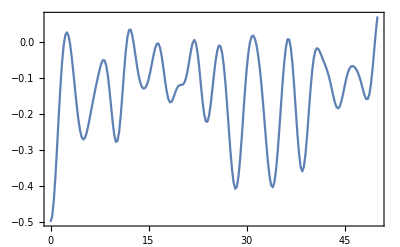

```mathematica
ListPlot[Szt,Frame->True,Joined->True,PlotRange->All]
```

### Minimizing parameters:

For 𝒫=1:

```mathematica
Clear[foo]
foo[θSeq___]:=With[{θ={θSeq}},
Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[n]]Heis[[n,Mod[n+1,L,1]]]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L,2}]]].init
];
```

For 𝒫=2:

```mathematica
Clear[foo]
foo[θSeq___]:=With[{θ={θSeq}},
Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[L+n]]Heis[[n,Mod[n+1,L,1]]]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[L+n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[n]]Heis[[n,Mod[n+1,L,1]]]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[MatrixExp[-ⅈ θ[[n]]Heis[[n,Mod[n+1,L,1]]]],{n,1,L,2}]]].init
]
```

```mathematica
Table[{n,n,Mod[n+1,L,1]},{n,1,L,2}]
Table[{n,n,Mod[n+1,L,1]},{n,2,L,2}]
```

{{1,1,2},{3,3,4},{5,5,1}}

{{2,2,3},{4,4,5}}

```mathematica
Table[{L+n,n,Mod[n+1,L,1]},{n,1,L,2}]
Table[{L+n,n,Mod[n+1,L,1]},{n,2,L,2}]
```

{{6,1,2},{8,3,4},{10,5,1}}

{{7,2,3},{9,4,5}}

```mathematica
vars=ToExpression[Table["φ"<>ToString[n],{n,1,𝒫*L}]];
```

```mathematica
vars
```

{φ1,φ2,φ3,φ4,φ5}

```mathematica
With[{θ={θ1,θ2,θ3,θ4,θ5,θ6,θ7,θ8,θ9,θ10}},Dot[Sequence@@Reverse[Table[f[-ⅈ θ[[L+n]]]*g[n,Mod[n+1,L,1]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[f[-ⅈ θ[[L+n]]]*g[n,Mod[n+1,L,1]],{n,1,L,2}]]].Dot[Sequence@@Reverse[Table[f[-ⅈ θ[[n]]]*g[n,Mod[n+1,L,1]],{n,2,L,2}]]].Dot[Sequence@@Reverse[Table[f[-ⅈ θ[[n]]]*g[n,Mod[n+1,L,1]],{n,1,L,2}]]].v0]
```

(f[-ⅈ θ9] g[4,5]).(f[-ⅈ θ7] g[2,3]).(f[-ⅈ θ10] g[5,1]).(f[-ⅈ θ8] g[3,4]).(f[-ⅈ θ6] g[1,2]).(f[-ⅈ θ4] g[4,5]).(f[-ⅈ θ2] g[2,3]).(f[-ⅈ θ5] g[5,1]).(f[-ⅈ θ3] g[3,4]).(f[-ⅈ θ1] g[1,2]).v0

```mathematica
varSzList1=Module[{tf,dt,Nt},
tf=50(*/Jp*);
dt=tf/200;
Nt=IntegerPart[tf/dt];
Table[{(t-1)dt,Block[{sol,bar},sol=NMinimize[1-Abs[Conjugate[ψ[[t]]].foo[Sequence@@vars]],vars][[2]]; bar=foo[Sequence@@vars]/.sol;
Conjugate[bar].Sz[[1]].bar/2]},{t,1,Length@ψ}]];
```

```mathematica
varSzList2=Module[{tf,dt,Nt},
tf=50(*/Jp*);
dt=tf/200;
Nt=IntegerPart[tf/dt];
Table[{(t-1)dt,Block[{sol,bar},sol=FindMinimum[1-Abs[Conjugate[ψ[[t]]].foo[Sequence@@vars]],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]][[2]]; bar=foo[Sequence@@vars]/.sol;
Conjugate[bar].Sz[[1]].bar/2]},{t,1,Length@ψ}]];
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindMinimum::lstol will be suppressed during this calculation.

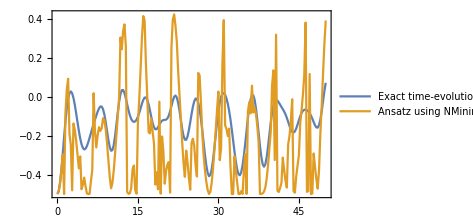
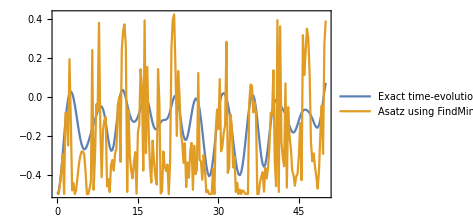
-Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[{Szt,varSzList1},Frame->True,PlotRange->All,Joined->True,FrameStyle->Directive[Black,FontSize->14],PlotLegends->{"Exact time-evolution","Ansatz using NMinimize"},ImageSize->350],ListPlot[{Szt,varSzList2},Frame->True,PlotRange->All,Joined->True,FrameStyle->Directive[Black,FontSize->14],PlotLegends->{"Exact time-evolution","Asatz using FindMinimum"},ImageSize->350]}}]
```

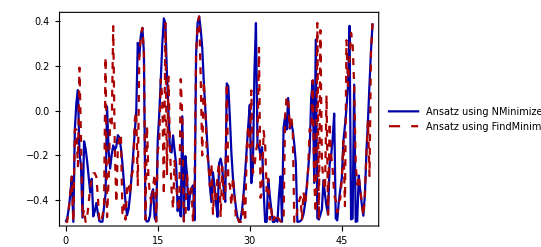

```mathematica
ListPlot[{varSzList1,varSzList2},Frame->True,PlotRange->All,Joined->True,FrameStyle->Directive[Black,FontSize->14],PlotLegends->{"Ansatz using NMinimize", "Ansatz using FindMinimum"},PlotStyle->{Directive[Darker[Blue]],Directive[Darker[Red],Dashed]}]
```

At t=0:

```mathematica
init
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ψ0=ψ[[1]]
```

{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
sol=NMinimize[1-Abs[Conjugate[ψ0].foo[Sequence@@vars]],vars]
```

{0.,{φ1→2.22577×10^-12,φ2→1.29759×10^-12,φ3→1.72495×10^-12,φ4→-2.94508×10^-12,φ5→0.343666}}

```mathematica
res1=Chop[vars/.sol[[2]]]
```

{0,0,0,0,0.343666}

```mathematica
sol2=FindMinimum[1-Abs[Conjugate[ψ0].foo[Sequence@@vars]],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{5.77316×10^-15,{φ1→3.92699,φ2→3.92699,φ3→0.785398,φ4→2.35619,φ5→3.92699}}

```mathematica
res2=Chop[vars/.sol2[[2]]]
```

{3.92699,3.92699,0.785398,2.35619,3.92699}

Initial state t=0.25s:

```mathematica
ψ1=ψ[[2]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.00769623-0.000157771 ⅈ,0.+0. ⅈ,-0.0153724-0.00128463 ⅈ,0.00763591-0.1225 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.0229277-0.119927 ⅈ,0.95191+0.181906 ⅈ,0.+0. ⅈ,0.00763591-0.1225 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.015332-0.00160573 ⅈ,0.0229277-0.119927 ⅈ,0.+0. ⅈ,-0.0153724-0.00128463 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.00769623-0.000157771 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
sol3=NMinimize[1-Abs[Conjugate[ψ1].foo[Sequence@@vars]],vars]
res3=Chop[vars/.sol3[[2]]]
```

{0.000278255,{φ1→0.0622499,φ2→0.0613262,φ3→0.0615846,φ4→0.0617523,φ5→0.0453585}}

{0.0622499,0.0613262,0.0615846,0.0617523,0.0453585}

```mathematica
sol4=FindMinimum[1-Abs[Conjugate[ψ1].foo[Sequence@@vars]],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]]
res4=Chop[vars/.sol4[[2]]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.00801575,{φ1→-0.723822,φ2→7.13015,φ3→13.3521,φ4→10.2719,φ5→-0.785532}}

{-0.723822,7.13015,13.3521,10.2719,-0.785532}

Initial state t=1.5s:

```mathematica
Position[Table[i,{i,0,50,50/200.}],1.50]
```

{{7}}

```mathematica
ψ2=ψ[[7]]
```

{0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.159195-0.0044845 ⅈ,0.+0. ⅈ,-0.301911-0.169364 ⅈ,0.108292-0.354028 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.337416+0.00336648 ⅈ,-0.00519012+0.306085 ⅈ,0.+0. ⅈ,0.108292-0.354028 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.263548-0.211153 ⅈ,0.337416+0.00336648 ⅈ,0.+0. ⅈ,-0.301911-0.169364 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,-0.159195-0.0044845 ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ,0.+0. ⅈ}

```mathematica
sol5=NMinimize[1-Abs[Conjugate[ψ2].foo[Sequence@@vars]],vars]
res5=Chop[vars/.sol5[[2]]]
```

{0.147812,{φ1→0.360212,φ2→0.220917,φ3→0.310407,φ4→0.373268,φ5→0.105839}}

{0.360212,0.220917,0.310407,0.373268,0.105839}

```mathematica
sol6=FindMinimum[1-Abs[Conjugate[ψ2].foo[Sequence@@vars]],Partition[Riffle[vars,RandomReal[{0,2π},Length@vars]],2]]
res6=Chop[vars/.sol6[[2]]]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{0.357028,{φ1→7.82747,φ2→6.5506,φ3→-2.85085,φ4→3.49315,φ5→4.07044}}

{7.82747,6.5506,-2.85085,3.49315,4.07044}

```mathematica
(*1->NMinimize
2->FindMinimum*)
vecφ1=res1; (*t=0, NMinimize*)
vecφ2=res2; (*t=0, FindMinimum*)
vecφ3=res3; (*t=0.25s, NMinimize*)
vecφ4=res4; (*t=0.25s, FindMinimum*)
vecφ5=res5; (*t=1.5s, NMinimize*)
vecφ6=res6; (*t=1.5s FindMinimum*)
ψvar1=KProd[vecφ1].init;
ψvar2=KProd[vecφ2].init;
ψvar3=KProd[vecφ3].init;
ψvar4=KProd[vecφ4].init;
ψvar5=KProd[vecφ5].init;
ψvar6=KProd[vecφ6].init;
(*ψvar1b=foo[Sequence@@vecφ1];
ψvar2b=foo[Sequence@@vecφ2];*)

Print["Initial state: ",init]
Print["variables for ansatz vecφ1 (NMinimize)= ",vecφ1]
Print["Corresponding ansatz: ",Chop[ψvar1]]
Print["variables for ansatz vecφ3 (NMinimize)= ",vecφ3]
Print["Corresponding ansatz: ",Chop[ψvar3]]
(*Print["Comparing: ", Chop[ψvar1b]];*)
Print["variables for ansatz vecφ2 (FindMinimum)= ",vecφ2]
Print["Corresponding ansatz: ",Chop[ψvar2]]
Print["variables for ansatz vecφ4 (FindMinimum)= ",vecφ4]
Print["Corresponding ansatz: ",Chop[ψvar4]]
(*Print["Comparing: ", Chop[ψvar2b]];*)
```

Initial state: {0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

variables for ansatz vecφ1 (NMinimize)= {0,0,0,0,0.343666}

Corresponding ansatz: {0,0,0,0,0,0,0,0,0,0,0.941526-0.336941 ⅈ,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

variables for ansatz vecφ3 (NMinimize)= {0.0622499,0.0613262,0.0615846,0.0617523,0.0453585}

Corresponding ansatz: {0,0,0,-0.0111526-0.000514661 ⅈ,0,-0.0149336-0.00166767 ⅈ,0.024097-0.117092 ⅈ,0,0,0.0242638-0.117914 ⅈ,0.950273+0.194147 ⅈ,0,-0.00543556-0.121786 ⅈ,0,0,0,0,-0.0149023-0.00255225 ⅈ,0.02056-0.120048 ⅈ,0,-0.0148652-0.00253285 ⅈ,0,0,0,-0.000312227+0.00183245 ⅈ,0,0,0,0,0,0,0}

variables for ansatz vecφ2 (FindMinimum)= {3.92699,3.92699,0.785398,2.35619,3.92699}

Corresponding ansatz: {0,0,0,1.10616×10^-8-1.10616×10^-8 ⅈ,0,0,4.02167×10^-8-4.02168×10^-8 ⅈ,0,0,2.422×10^-8-2.42201×10^-8 ⅈ,-0.707107-0.707107 ⅈ,0,4.12088×10^-8-4.12088×10^-8 ⅈ,0,0,0,0,0,0,0,0,0,0,0,4.20244×10^-8-4.20245×10^-8 ⅈ,0,0,0,0,0,0,0}

variables for ansatz vecφ4 (FindMinimum)= {-0.723822,7.13015,13.3521,10.2719,-0.785532}

Corresponding ansatz: {0,0,0,0.000448624+0.000396526 ⅈ,0,0.0124487-0.0085229 ⅈ,0.0683316+0.0998062 ⅈ,0,0,0.0685275+0.100092 ⅈ,-0.806504+0.552167 ⅈ,0,0.0920198+0.0813776 ⅈ,0,0,0,0,-1.1946×10^-7+1.05512×10^-7 ⅈ,1.30957×10^-8+1.48269×10^-8 ⅈ,0,-0.0000244989+0.0000216537 ⅈ,0,0,0,-0.000174964-0.000197953 ⅈ,0,0,0,0,0,0,0}

## Variational calculation of φ_j(t) - Solving the differential equation

```mathematica
(*Create a diagonal matrix, which is a small number times identity that should be added to A in roder to make it not singular*)

Amatrix[O_,ϵ_,φvec_]:=Module[{dim,A,vecaux,ket,mdepth,sitei,Smdag,Opm,ketm,bram,cm,ndepth,sitej,Sndag,Opn,ketn,bran,cn,e,vφ},
e=ϵ;
dim=L*𝒫;
A={};
vφ=φvec;
ket=KProd[vφ].init;
Do[
{mdepth,sitei}=Convert[i,L];
Smdag=ConjugateTranspose[OpS[mdepth,sitei,vφ]];
Opm=Smdag.O;
ketm=KLesser[mdepth,vφ].init;
bram=Conjugate[ketm];

cm=Im[bram.Opm.ket];
vecaux={};
Do[
{ndepth,sitej}=Convert[j,L];
Sndag=ConjugateTranspose[OpS[ndepth,sitej,vφ]];
Opn=Sndag.O;
ketn=KLesser[ndepth,vφ].init;
bran=Conjugate[ketn];

cn=Im[bran.Opn.ket];

AppendTo[vecaux,2*cm*cn];
,{j,1,dim}];
AppendTo[A,vecaux];
,{i,1,dim}];

A=A+(e*IdentityMatrix[dim]);
A
];

Bvector[O_,φvec_]:=Module[{dim,B,ket,bra,mdepth,sitei,Smdag,Opm,ketm,bram,cm,Commutator,dm,H,vφ},
dim=L*𝒫;
B={};
vφ=φvec;
ket=KProd[vφ].init;
bra=Conjugate[ket];
H=(Sum[Heis[[i,Mod[i+1,L,1]]],{i,1,L}])/4;
Commutator=(O.H-H.O);

Do[
{mdepth,sitei}=Convert[i,L];
Smdag=ConjugateTranspose[OpS[mdepth,sitei,vφ]];
Opm=Smdag.O;
ketm=KLesser[mdepth,vφ].init;
bram=Conjugate[ketm];

cm=Im[bram.Opm.ket];


dm=Im[bra.Commutator.ket];

AppendTo[B,(-1)*cm*dm];

,{i,1,dim}];

B

];
```

### Checking the derivatives

i_pos can be any number between 1 and L𝒫

```mathematica
Deriv[O_,φvec_]:=Module[{vφ,dim,A,vecaux,ket,mdepth,sitei,Smdag,Opm,ketm,bram,cm},
dim=L*𝒫;
A={};
vφ=φvec;
ket=KProd[vφ].init;

Do[
{mdepth,sitei}=Convert[i,L];
Smdag=ConjugateTranspose[OpS[mdepth,sitei,vφ]];
Opm=Smdag.O;
ketm=KLesser[mdepth,vφ].init;
bram=Conjugate[ketm];
cm=(-2)*Im[bram.Opm.ket];
AppendTo[A,cm];
,{i,1,dim}];
A
];
```

```mathematica
Deriv[Sz[[1]],{φ1,φ2,φ3,φ4,φ5}]
```

$Aborted

```mathematica
Ld1=ParallelTable[{φ1,Deriv[Sz[[1]],{φ1,0,0,0,0}][[1]]},{φ1,0,2*Pi,0.01*Pi}];
Ld2=ParallelTable[{φ2,Deriv[Sz[[1]],{0,φ2,0,0,0}][[2]]},{φ2,0,2*Pi,0.01*Pi}];
Ld3=ParallelTable[{φ3,Deriv[Sz[[1]],{0,0,φ3,0,0}][[3]]},{φ3,0,2*Pi,0.01*Pi}];
Ld4=ParallelTable[{φ4,Deriv[Sz[[1]],{0,0,0,φ4,0}][[4]]},{φ4,0,2*Pi,0.01*Pi}];
Ld5=ParallelTable[{φ5,Deriv[Sz[[1]],{0,0,0,0,φ5}][[5]]},{φ5,0,2*Pi,0.01*Pi}];
```

```mathematica
fLd1=ListPlot[Ld1,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_1","dS_(z, 1)/dφ_1"},PlotLabel->"φ_2=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Red]];
fLd2=ListPlot[Ld2,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_2","dS_(z, 1)/dφ_2"},PlotLabel->"φ_1=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Blue]];
fLd3=ListPlot[Ld3,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_3","dS_(z, 1)/dφ_3"},PlotLabel->"φ_1=φ_2=φ_4=φ_5=0",ImageSize->350,PlotStyle->Purple];
fLd4=ListPlot[Ld4,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_4","dS_(z, 1)/dφ_4"},PlotLabel->"φ_1=φ_2=φ_3=φ_5=0",ImageSize->350,PlotStyle->Darker[Cyan]];
fLd5=ListPlot[Ld5,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_5","dS_(z, 1)/dφ_5"},PlotLabel->"φ_1=φ_2=φ_3=φ_4=0",ImageSize->350,PlotStyle->Darker[Green]];
```

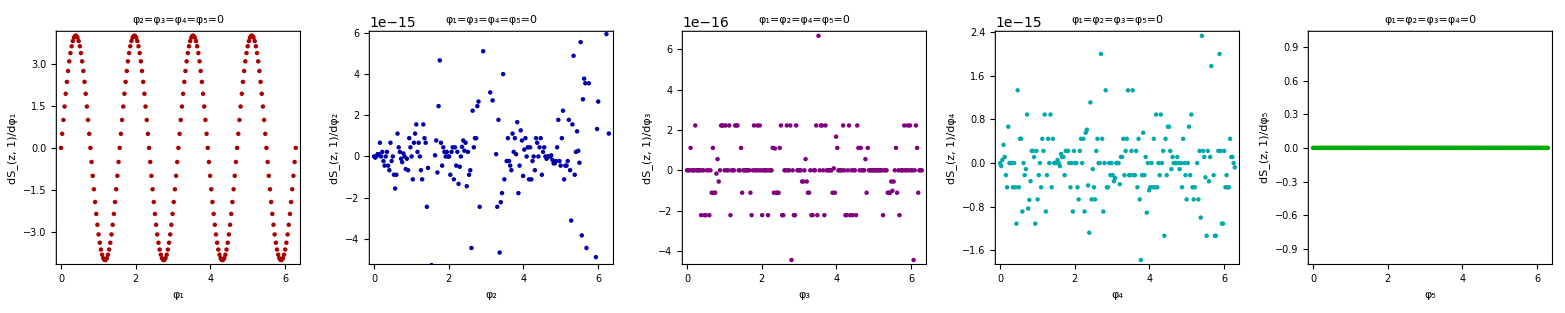

```mathematica
Grid[{{fLd1,fLd2,fLd3,fLd4,fLd5}},Spacings->3]
```

```mathematica
Ld1=ParallelTable[{φ1,Deriv[Sz[[2]],{φ1,0,0,0,0}][[1]]},{φ1,0,2*Pi,0.01*Pi}];
Ld2=ParallelTable[{φ2,Deriv[Sz[[2]],{0,φ2,0,0,0}][[2]]},{φ2,0,2*Pi,0.01*Pi}];
Ld3=ParallelTable[{φ3,Deriv[Sz[[2]],{0,0,φ3,0,0}][[3]]},{φ3,0,2*Pi,0.01*Pi}];
Ld4=ParallelTable[{φ4,Deriv[Sz[[2]],{0,0,0,φ4,0}][[4]]},{φ4,0,2*Pi,0.01*Pi}];
Ld5=ParallelTable[{φ5,Deriv[Sz[[2]],{0,0,0,0,φ5}][[5]]},{φ5,0,2*Pi,0.01*Pi}];
```

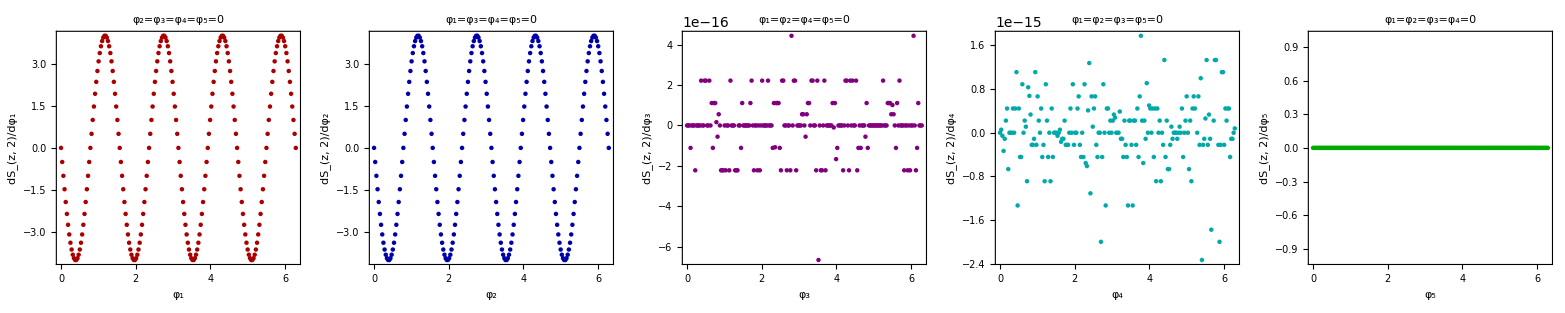

```mathematica
fLd1=ListPlot[Ld1,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_1","dS_(z, 2)/dφ_1"},PlotLabel->"φ_2=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Red]];
fLd2=ListPlot[Ld2,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_2","dS_(z, 2)/dφ_2"},PlotLabel->"φ_1=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Blue]];
fLd3=ListPlot[Ld3,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_3","dS_(z, 2)/dφ_3"},PlotLabel->"φ_1=φ_2=φ_4=φ_5=0",ImageSize->350,PlotStyle->Purple];
fLd4=ListPlot[Ld4,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_4","dS_(z, 2)/dφ_4"},PlotLabel->"φ_1=φ_2=φ_3=φ_5=0",ImageSize->350,PlotStyle->Darker[Cyan]];
fLd5=ListPlot[Ld5,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_5","dS_(z, 2)/dφ_5"},PlotLabel->"φ_1=φ_2=φ_3=φ_4=0",ImageSize->350,PlotStyle->Darker[Green]];
Grid[{{fLd1,fLd2,fLd3,fLd4,fLd5}},Spacings->3]
```

```mathematica
Ld1=ParallelTable[{φ1,Deriv[Sz[[3]],{φ1,0,0,0,0}][[1]]},{φ1,0,2*Pi,0.01*Pi}];
Ld2=ParallelTable[{φ2,Deriv[Sz[[3]],{0,φ2,0,0,0}][[2]]},{φ2,0,2*Pi,0.01*Pi}];
Ld3=ParallelTable[{φ3,Deriv[Sz[[3]],{0,0,φ3,0,0}][[3]]},{φ3,0,2*Pi,0.01*Pi}];
Ld4=ParallelTable[{φ4,Deriv[Sz[[3]],{0,0,0,φ4,0}][[4]]},{φ4,0,2*Pi,0.01*Pi}];
Ld5=ParallelTable[{φ5,Deriv[Sz[[3]],{0,0,0,0,φ5}][[5]]},{φ5,0,2*Pi,0.01*Pi}];
```

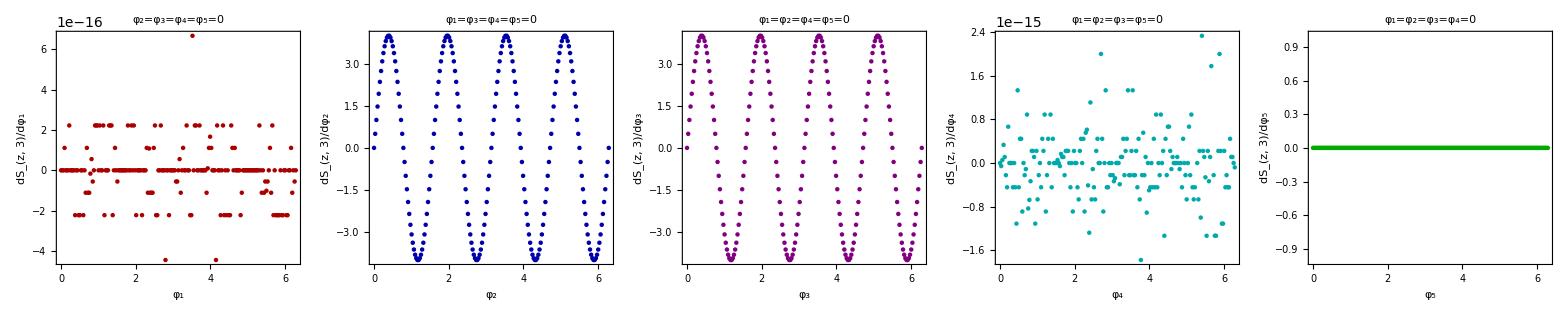

```mathematica
fLd1=ListPlot[Ld1,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_1","dS_(z, 3)/dφ_1"},PlotLabel->"φ_2=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Red]];
fLd2=ListPlot[Ld2,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_2","dS_(z, 3)/dφ_2"},PlotLabel->"φ_1=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Blue]];
fLd3=ListPlot[Ld3,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_3","dS_(z, 3)/dφ_3"},PlotLabel->"φ_1=φ_2=φ_4=φ_5=0",ImageSize->350,PlotStyle->Purple];
fLd4=ListPlot[Ld4,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_4","dS_(z, 3)/dφ_4"},PlotLabel->"φ_1=φ_2=φ_3=φ_5=0",ImageSize->350,PlotStyle->Darker[Cyan]];
fLd5=ListPlot[Ld5,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_5","dS_(z, 3)/dφ_5"},PlotLabel->"φ_1=φ_2=φ_3=φ_4=0",ImageSize->350,PlotStyle->Darker[Green]];
Grid[{{fLd1,fLd2,fLd3,fLd4,fLd5}},Spacings->3]
```

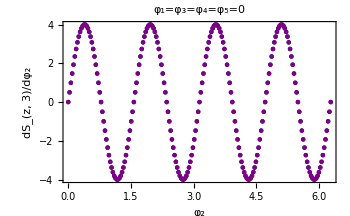

```mathematica
Show[fLd2,fLd3]
```

```mathematica
Ld1=ParallelTable[{φ1,Deriv[Sz[[4]],{φ1,0,0,0,0}][[1]]},{φ1,0,2*Pi,0.01*Pi}];
Ld2=ParallelTable[{φ2,Deriv[Sz[[4]],{0,φ2,0,0,0}][[2]]},{φ2,0,2*Pi,0.01*Pi}];
Ld3=ParallelTable[{φ3,Deriv[Sz[[4]],{0,0,φ3,0,0}][[3]]},{φ3,0,2*Pi,0.01*Pi}];
Ld4=ParallelTable[{φ4,Deriv[Sz[[4]],{0,0,0,φ4,0}][[4]]},{φ4,0,2*Pi,0.01*Pi}];
Ld5=ParallelTable[{φ5,Deriv[Sz[[4]],{0,0,0,0,φ5}][[5]]},{φ5,0,2*Pi,0.01*Pi}];
```

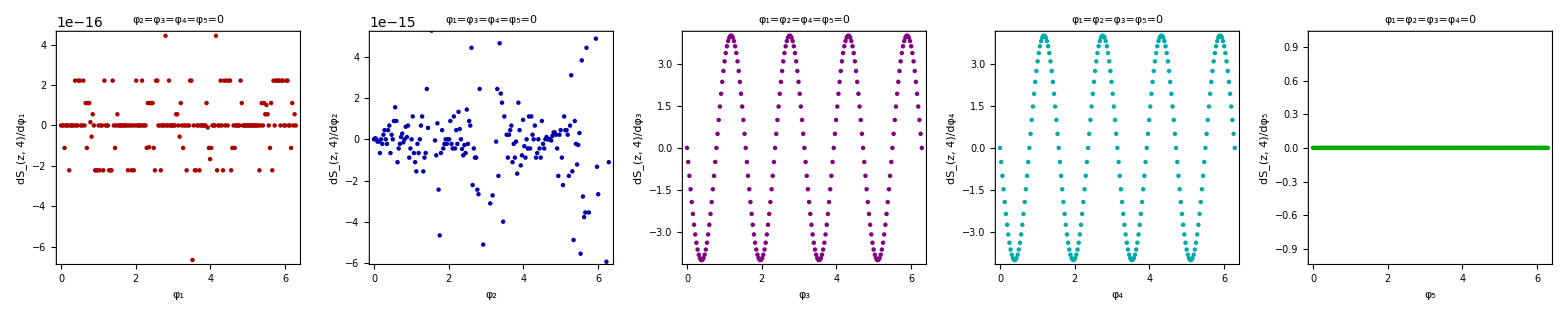

```mathematica
fLd1=ListPlot[Ld1,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_1","dS_(z, 4)/dφ_1"},PlotLabel->"φ_2=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Red]];
fLd2=ListPlot[Ld2,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_2","dS_(z, 4)/dφ_2"},PlotLabel->"φ_1=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Blue]];
fLd3=ListPlot[Ld3,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_3","dS_(z, 4)/dφ_3"},PlotLabel->"φ_1=φ_2=φ_4=φ_5=0",ImageSize->350,PlotStyle->Purple];
fLd4=ListPlot[Ld4,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_4","dS_(z, 4)/dφ_4"},PlotLabel->"φ_1=φ_2=φ_3=φ_5=0",ImageSize->350,PlotStyle->Darker[Cyan]];
fLd5=ListPlot[Ld5,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_5","dS_(z, 4)/dφ_5"},PlotLabel->"φ_1=φ_2=φ_3=φ_4=0",ImageSize->350,PlotStyle->Darker[Green]];
Grid[{{fLd1,fLd2,fLd3,fLd4,fLd5}},Spacings->3]
```

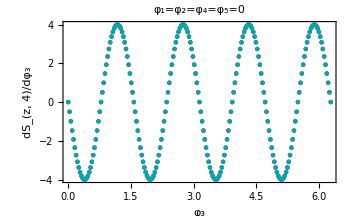

```mathematica
Show[fLd3,fLd4]
```

```mathematica
Ld1=ParallelTable[{φ1,Deriv[Sz[[5]],{φ1,0,0,0,0}][[1]]},{φ1,0,2*Pi,0.01*Pi}];
Ld2=ParallelTable[{φ2,Deriv[Sz[[5]],{0,φ2,0,0,0}][[2]]},{φ2,0,2*Pi,0.01*Pi}];
Ld3=ParallelTable[{φ3,Deriv[Sz[[5]],{0,0,φ3,0,0}][[3]]},{φ3,0,2*Pi,0.01*Pi}];
Ld4=ParallelTable[{φ4,Deriv[Sz[[5]],{0,0,0,φ4,0}][[4]]},{φ4,0,2*Pi,0.01*Pi}];
Ld5=ParallelTable[{φ5,Deriv[Sz[[5]],{0,0,0,0,φ5}][[5]]},{φ5,0,2*Pi,0.01*Pi}];
```

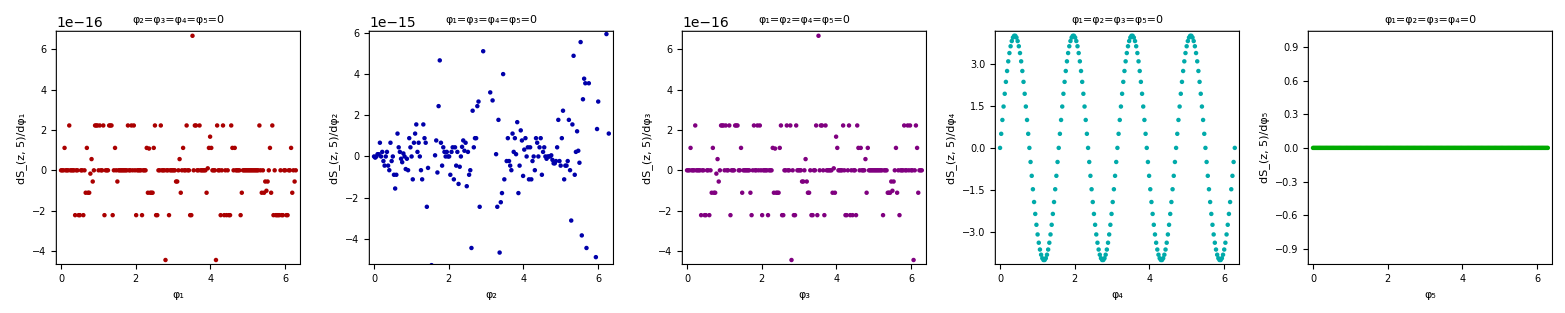

```mathematica
fLd1=ListPlot[Ld1,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_1","dS_(z, 5)/dφ_1"},PlotLabel->"φ_2=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Red]];
fLd2=ListPlot[Ld2,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_2","dS_(z, 5)/dφ_2"},PlotLabel->"φ_1=φ_3=φ_4=φ_5=0",ImageSize->350,PlotStyle->Darker[Blue]];
fLd3=ListPlot[Ld3,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_3","dS_(z, 5)/dφ_3"},PlotLabel->"φ_1=φ_2=φ_4=φ_5=0",ImageSize->350,PlotStyle->Purple];
fLd4=ListPlot[Ld4,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_4","dS_(z, 5)/dφ_4"},PlotLabel->"φ_1=φ_2=φ_3=φ_5=0",ImageSize->350,PlotStyle->Darker[Cyan]];
fLd5=ListPlot[Ld5,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"φ_5","dS_(z, 5)/dφ_5"},PlotLabel->"φ_1=φ_2=φ_3=φ_4=0",ImageSize->350,PlotStyle->Darker[Green]];
Grid[{{fLd1,fLd2,fLd3,fLd4,fLd5}},Spacings->3]
```

```mathematica
{Convert[1,L],Convert[2,L],Convert[3,L],Convert[4,L],Convert[5,L]}
```

{{1,1},{1,2},{1,3},{1,4},{1,5}}

```mathematica
A1=Heis[[2,3]];
B1=Heis[[4,5]];
```

```mathematica
(A1.B1-B1.A1)//MatrixForm
```

(0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

## Solution of the differential equation for φ_j(t)

```mathematica
φsol[tinitial_,tfinal_,increment_,O_,φ0_,epsilon_]:=Module[{t0,tf,Δt,LocalOp,vφ0,ϵ,Mres,Gridt,φaux,t,Aaux,Aauxinv,Baux,φnext},
t0=tinitial;
tf=tfinal;
Δt=increment;
LocalOp=O;
vφ0=φ0;
ϵ=epsilon; (*quantity to be added to A so it is no longer singular*)
Mres={{t0,vφ0}}; (*Stores the vector of variables φ for each time step*)

(*Define grid for t*)
Gridt=Table[j,{j,t0+Δt,tf,Δt}]; (*starts at Subscript[t, 0]+Δt*)
Print["Total of points: ",Length[Gridt]];

(*At each t:
1) Contruct A matrix and B vector for the variable vector φ(t) correspondent to this time t. Recalling that φ for t=0 was constructed outside of this function;
	 2) Contruct φ(t+Δt)=φ(t)+Δt*(A^-1(t)B(t));
        3) Store φ(t)
*)

φaux=vφ0;

Do[
t=Gridt[[i]];
Aaux=Amatrix[LocalOp,ϵ,φaux];
Aauxinv=Inverse[Aaux];
Baux=Bvector[LocalOp,φaux];
φnext=φaux+(Δt*(Aauxinv.Baux));
φaux=φnext;
AppendTo[Mres,{t,φaux}];
If[Mod[i,30]==0,Print[i]];

,{i,1,Length[Gridt]}];

Mres
]
```

```mathematica
Resφ=φsol[0.25,50,0.25,Sz[[1]],vecφ3,10^-5];
Resφ2=φsol[0.25,50,0.25,Sz[[1]],vecφ4,10^-5];
```

Total of points: 199

30

60

90

120

150

180

Total of points: 199

30

60

90

120

150

180

```mathematica
Resφ3=φsol[1.5,50,0.25,Sz[[1]],vecφ5,10^-5];
Resφ4=φsol[1.5,50,0.25,Sz[[1]],vecφ6,10^-5];
```

Total of points: 194

30

60

90

120

150

180

Total of points: 194

30

60

90

120

150

180

```mathematica
Length[Resφ]
```

200

```mathematica
Resφ[[1]]
```

{0.25,{0.0622499,0.0613262,0.0615846,0.0617523,0.0453585}}

```mathematica
φ1c1=Table[{Resφ[[i,1]],Resφ[[i,2]][[1]]},{i,1,Length[Resφ]}];
φ1c2=Table[{Resφ[[i,1]],Resφ[[i,2]][[2]]},{i,1,Length[Resφ]}];
φ1c3=Table[{Resφ[[i,1]],Resφ[[i,2]][[3]]},{i,1,Length[Resφ]}];
φ1c4=Table[{Resφ[[i,1]],Resφ[[i,2]][[4]]},{i,1,Length[Resφ]}];
φ1c5=Table[{Resφ[[i,1]],Resφ[[i,2]][[5]]},{i,1,Length[Resφ]}];
```

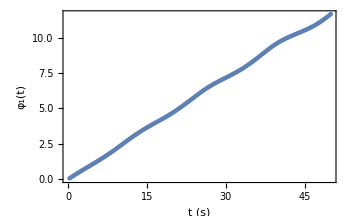
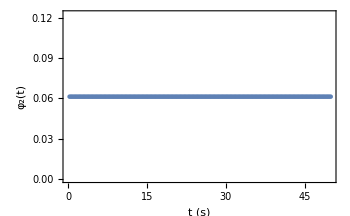
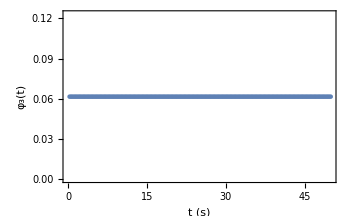
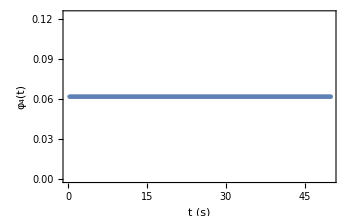
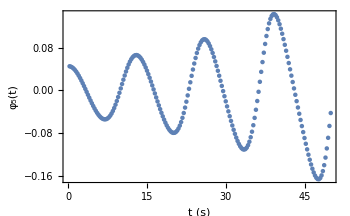
-Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- |

```mathematica
Grid[{{ListPlot[φ1c1,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_1(t)"},ImageSize->350],ListPlot[φ1c2,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_2(t)"},ImageSize->350],ListPlot[φ1c3,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_3(t)"},ImageSize->350]},{ListPlot[φ1c4,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_4(t)"},ImageSize->350],ListPlot[φ1c5,Frame->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_5(t)"},ImageSize->350]}}]
```

```mathematica
Oexpect[O_,M_]:=Module[{Mres,Op,Ltot,Res,taux,vecaux,valaux,ket,bra},
Op=O;
Mres=M;
Ltot=Length[Mres];(*number of t ponts*)
Res={};
Do[
taux=Mres[[i,1]];
vecaux=Mres[[i,2]];
ket=KProd[vecaux].init;
bra=Conjugate[ket];
valaux=bra.Op.ket/2;
AppendTo[Res,{taux,valaux}];
,{i,1,Ltot}];
Res
]
```

```mathematica
Test=Oexpect[Sz[[1]],Resφ];
```

```mathematica
Test2=Oexpect[Sz[[1]],Resφ2];
```

```mathematica
Test3=Oexpect[Sz[[1]],Resφ3];
Test4=Oexpect[Sz[[1]],Resφ4];
```

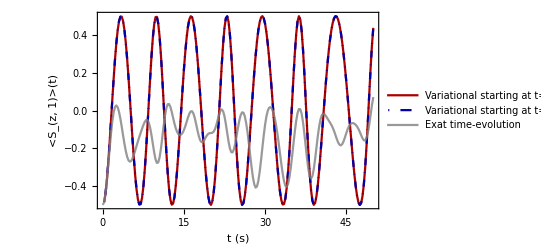

```mathematica
ListPlot[{Test,Test2,Szt},Frame->True,Joined->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","<S_(z, 1)>(t)"},PlotLegends->{"Variational starting at t=0.25s (Nminimize)", "Variational starting at t=0.25s (FindMinimum)","Exat time-evolution"},PlotStyle->{Directive[Darker[Red]],Directive[DotDashed,Darker[Blue]],Directive[Thick,Gray,Opacity[0.8]]}]
```

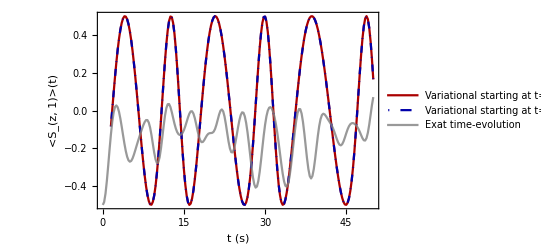

```mathematica
ListPlot[{Test3,Test4,Szt},Frame->True,Joined->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","<S_(z, 1)>(t)"},PlotLegends->{"Variational starting at t=1.5s (Nminimize)", "Variational starting at t=1.5s (FindMinimum)","Exat time-evolution"},PlotStyle->{Directive[Darker[Red]],Directive[DotDashed,Darker[Blue]],Directive[Thick,Gray,Opacity[0.8]]}]
```

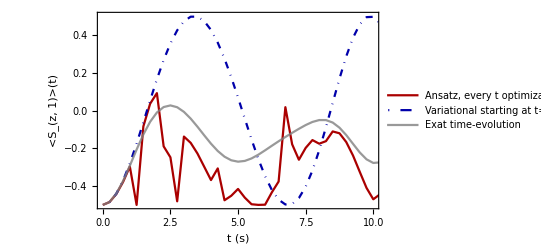

```mathematica
ListPlot[{varSzList1,Test2,Szt},Frame->True,Joined->True,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","<S_(z, 1)>(t)"},PlotLegends->{"Ansatz, every t optimization", "Variational starting at t=0.25s (FindMinimum)","Exat time-evolution"},PlotStyle->{Directive[Darker[Red]],Directive[DotDashed,Darker[Blue]],Directive[Thick,Gray,Opacity[0.8]]},PlotRange->{{0,10},Automatic}]
```

### tests

```mathematica
Clear[Test]
```

```mathematica
Test;
```

```mathematica
Test=AbsoluteTiming[φsol[0,10,0.1,Sz[[1]],φansatznum,10^-5]]
```

{67.1011,{{0,{2.28884,5.31863,1.90306,3.37893,1.91114,5.19267,4.17135,2.48099,0.563401,2.03598}},{0.1,{2.28346,5.31863,1.90306,3.37893,1.91165,5.19093,4.19214,2.48099,0.562442,2.03708}},{0.2,{2.27815,5.31863,1.90306,3.37893,1.91219,5.18902,4.21297,2.48099,0.561444,2.03823}},{0.3,{2.27295,5.31863,1.90306,3.37893,1.91274,5.18693,4.23386,2.48099,0.560414,2.03941}},{0.4,{2.26786,5.31863,1.90306,3.37893,1.91331,5.18465,4.25481,2.48099,0.559363,2.04062}},{0.5,{2.26291,5.31863,1.90306,3.37893,1.91386,5.18217,4.27581,2.48099,0.558302,2.04184}},{0.6,{2.25813,5.31863,1.90306,3.37893,1.9144,5.17947,4.29687,2.48099,0.557241,2.04306}},{0.7,{2.25353,5.31863,1.90306,3.37893,1.91489,5.17654,4.31797,2.48099,0.556195,2.04427}},{0.8,{2.24916,5.31863,1.90306,3.37893,1.91532,5.17335,4.33912,2.48099,0.555178,2.04544}},{0.9,{2.24503,5.31863,1.90306,3.37893,1.91567,5.16988,4.3603,2.48099,0.554207,2.04657}},{1.,{2.24118,5.31863,1.90306,3.37893,1.91591,5.1661,4.38148,2.48099,0.553299,2.04763}},{1.1,{2.23764,5.31863,1.90306,3.37893,1.91602,5.16199,4.40261,2.48099,0.552474,2.0486}},{1.2,{2.23444,5.31863,1.90306,3.37893,1.91595,5.1575,4.42367,2.48099,0.551753,2.04946}},{1.3,{2.23163,5.31863,1.90306,3.37893,1.91568,5.1526,4.44457,2.48099,0.551159,2.05019}},{1.4,{2.22923,5.31863,1.90306,3.37893,1.91517,5.14725,4.46521,2.48099,0.550714,2.05076}},{1.5,{2.22727,5.31863,1.90306,3.37893,1.91438,5.14143,4.4855,2.48099,0.550441,2.05116}},{1.6,{2.22576,5.31863,1.90306,3.37893,1.9133,5.1351,4.50527,2.48099,0.550358,2.05135}},{1.7,{2.2247,5.31863,1.90306,3.37893,1.91188,5.12826,4.52434,2.48099,0.550479,2.05133}},{1.8,{2.2241,5.31863,1.90306,3.37893,1.91013,5.12093,4.54253,2.48099,0.550809,2.05108}},{1.9,{2.2239,5.31863,1.90306,3.37893,1.90806,5.11316,4.55961,2.48099,0.551342,2.05062}},{2.,{2.22405,5.31863,1.90306,3.37893,1.90569,5.10505,4.57539,2.48099,0.552059,2.04996}},{2.1,{2.22449,5.31863,1.90306,3.37893,1.90308,5.09673,4.5897,2.48099,0.552926,2.04913}},{2.2,{2.22512,5.31863,1.90306,3.37893,1.90031,5.08837,4.60244,2.48099,0.553901,2.04817}},{2.3,{2.22587,5.31863,1.90306,3.37893,1.89747,5.08015,4.61359,2.48099,0.554936,2.04713}},{2.4,{2.22667,5.31863,1.90306,3.37893,1.89463,5.07223,4.62321,2.48099,0.555986,2.04606}},{2.5,{2.22746,5.31863,1.90306,3.37893,1.89186,5.06472,4.63144,2.48099,0.557015,2.045}},{2.6,{2.22822,5.31863,1.90306,3.37893,1.88921,5.05772,4.63842,2.48099,0.557998,2.04397}},{2.7,{2.22893,5.31863,1.90306,3.37893,1.88673,5.05126,4.64433,2.48099,0.558917,2.043}},{2.8,{2.22957,5.31863,1.90306,3.37893,1.88441,5.04535,4.64933,2.48099,0.559765,2.0421}},{2.9,{2.23015,5.31863,1.90306,3.37893,1.88227,5.03996,4.65359,2.48099,0.560541,2.04126}},{3.,{2.23067,5.31863,1.90306,3.37893,1.88031,5.03508,4.65721,2.48099,0.561246,2.0405}},{3.1,{2.23114,5.31863,1.90306,3.37893,1.87851,5.03066,4.66031,2.48099,0.561884,2.0398}},{3.2,{2.23155,5.31863,1.90306,3.37893,1.87687,5.02666,4.66298,2.48099,0.562461,2.03916}},{3.3,{2.23192,5.31863,1.90306,3.37893,1.87538,5.02304,4.66529,2.48099,0.562981,2.03859}},{3.4,{2.23225,5.31863,1.90306,3.37893,1.87401,5.01977,4.6673,2.48099,0.563452,2.03806}},{3.5,{2.23255,5.31863,1.90306,3.37893,1.87277,5.01681,4.66906,2.48099,0.563876,2.03759}},{3.6,{2.23281,5.31863,1.90306,3.37893,1.87163,5.01412,4.6706,2.48099,0.56426,2.03716}},{3.7,{2.23305,5.31863,1.90306,3.37893,1.8706,5.01169,4.67195,2.48099,0.564607,2.03677}},{3.8,{2.23327,5.31863,1.90306,3.37893,1.86966,5.00947,4.67315,2.48099,0.564922,2.03641}},{3.9,{2.23346,5.31863,1.90306,3.37893,1.86879,5.00746,4.67422,2.48099,0.565207,2.03609}},{4.,{2.23364,5.31863,1.90306,3.37893,1.86801,5.00563,4.67516,2.48099,0.565466,2.03579}},{4.1,{2.2338,5.31863,1.90306,3.37893,1.86729,5.00397,4.67601,2.48099,0.565702,2.03552}},{4.2,{2.23394,5.31863,1.90306,3.37893,1.86663,5.00244,4.67677,2.48099,0.565916,2.03528}},{4.3,{2.23407,5.31863,1.90306,3.37893,1.86602,5.00106,4.67745,2.48099,0.566112,2.03505}},{4.4,{2.23419,5.31863,1.90306,3.37893,1.86547,4.99979,4.67806,2.48099,0.56629,2.03485}},{4.5,{2.2343,5.31863,1.90306,3.37893,1.86496,4.99863,4.67862,2.48099,0.566452,2.03466}},{4.6,{2.2344,5.31863,1.90306,3.37893,1.8645,4.99757,4.67912,2.48099,0.566601,2.03449}},{4.7,{2.23449,5.31863,1.90306,3.37893,1.86407,4.9966,4.67957,2.48099,0.566737,2.03433}},{4.8,{2.23457,5.31863,1.90306,3.37893,1.86368,4.9957,4.67998,2.48099,0.566861,2.03419}},{4.9,{2.23465,5.31863,1.90306,3.37893,1.86332,4.99489,4.68036,2.48099,0.566975,2.03406}},{5.,{2.23472,5.31863,1.90306,3.37893,1.86298,4.99414,4.68069,2.48099,0.567079,2.03394}},{5.1,{2.23478,5.31863,1.90306,3.37893,1.86268,4.99345,4.681,2.48099,0.567175,2.03383}},{5.2,{2.23484,5.31863,1.90306,3.37893,1.8624,4.99282,4.68129,2.48099,0.567262,2.03372}},{5.3,{2.23489,5.31863,1.90306,3.37893,1.86214,4.99224,4.68154,2.48099,0.567343,2.03363}},{5.4,{2.23494,5.31863,1.90306,3.37893,1.8619,4.9917,4.68178,2.48099,0.567417,2.03354}},{5.5,{2.23499,5.31863,1.90306,3.37893,1.86168,4.99121,4.68199,2.48099,0.567485,2.03347}},{5.6,{2.23503,5.31863,1.90306,3.37893,1.86148,4.99076,4.68219,2.48099,0.567548,2.03339}},{5.7,{2.23507,5.31863,1.90306,3.37893,1.8613,4.99034,4.68237,2.48099,0.567605,2.03333}},{5.8,{2.2351,5.31863,1.90306,3.37893,1.86113,4.98996,4.68254,2.48099,0.567658,2.03326}},{5.9,{2.23514,5.31863,1.90306,3.37893,1.86097,4.98961,4.68269,2.48099,0.567707,2.03321}},{6.,{2.23517,5.31863,1.90306,3.37893,1.86082,4.98928,4.68283,2.48099,0.567752,2.03315}},{6.1,{2.23519,5.31863,1.90306,3.37893,1.86069,4.98898,4.68296,2.48099,0.567793,2.03311}},{6.2,{2.23522,5.31863,1.90306,3.37893,1.86057,4.98871,4.68307,2.48099,0.567831,2.03306}},{6.3,{2.23524,5.31863,1.90306,3.37893,1.86045,4.98845,4.68318,2.48099,0.567866,2.03302}},{6.4,{2.23526,5.31863,1.90306,3.37893,1.86035,4.98822,4.68328,2.48099,0.567898,2.03298}},{6.5,{2.23528,5.31863,1.90306,3.37893,1.86025,4.988,4.68337,2.48099,0.567928,2.03295}},{6.6,{2.2353,5.31863,1.90306,3.37893,1.86016,4.9878,4.68346,2.48099,0.567956,2.03292}},{6.7,{2.23532,5.31863,1.90306,3.37893,1.86008,4.98762,4.68353,2.48099,0.567981,2.03289}},{6.8,{2.23533,5.31863,1.90306,3.37893,1.86,4.98745,4.6836,2.48099,0.568004,2.03286}},{6.9,{2.23535,5.31863,1.90306,3.37893,1.85993,4.98729,4.68367,2.48099,0.568026,2.03283}},{7.,{2.23536,5.31863,1.90306,3.37893,1.85987,4.98715,4.68373,2.48099,0.568046,2.03281}},{7.1,{2.23537,5.31863,1.90306,3.37893,1.8598,4.98701,4.68379,2.48099,0.568064,2.03279}},{7.2,{2.23538,5.31863,1.90306,3.37893,1.85975,4.98689,4.68384,2.48099,0.568081,2.03277}},{7.3,{2.2354,5.31863,1.90306,3.37893,1.8597,4.98677,4.68388,2.48099,0.568097,2.03275}},{7.4,{2.2354,5.31863,1.90306,3.37893,1.85965,4.98667,4.68393,2.48099,0.568111,2.03273}},{7.5,{2.23541,5.31863,1.90306,3.37893,1.85961,4.98657,4.68397,2.48099,0.568125,2.03272}},{7.6,{2.23542,5.31863,1.90306,3.37893,1.85957,4.98648,4.68401,2.48099,0.568137,2.0327}},{7.7,{2.23543,5.31863,1.90306,3.37893,1.85953,4.9864,4.68404,2.48099,0.568148,2.03269}},{7.8,{2.23544,5.31863,1.90306,3.37893,1.85949,4.98632,4.68407,2.48099,0.568159,2.03268}},{7.9,{2.23544,5.31863,1.90306,3.37893,1.85946,4.98625,4.6841,2.48099,0.568169,2.03267}},{8.,{2.23545,5.31863,1.90306,3.37893,1.85943,4.98619,4.68413,2.48099,0.568178,2.03266}},{8.1,{2.23545,5.31863,1.90306,3.37893,1.85941,4.98613,4.68415,2.48099,0.568186,2.03265}},{8.2,{2.23546,5.31863,1.90306,3.37893,1.85938,4.98607,4.68418,2.48099,0.568193,2.03264}},{8.3,{2.23546,5.31863,1.90306,3.37893,1.85936,4.98602,4.6842,2.48099,0.568201,2.03263}},{8.4,{2.23547,5.31863,1.90306,3.37893,1.85934,4.98597,4.68422,2.48099,0.568207,2.03262}},{8.5,{2.23547,5.31863,1.90306,3.37893,1.85932,4.98593,4.68424,2.48099,0.568213,2.03261}},{8.6,{2.23548,5.31863,1.90306,3.37893,1.8593,4.98589,4.68425,2.48099,0.568219,2.03261}},{8.7,{2.23548,5.31863,1.90306,3.37893,1.85928,4.98585,4.68427,2.48099,0.568224,2.0326}},{8.8,{2.23548,5.31863,1.90306,3.37893,1.85927,4.98582,4.68428,2.48099,0.568229,2.0326}},{8.9,{2.23549,5.31863,1.90306,3.37893,1.85925,4.98578,4.68429,2.48099,0.568233,2.03259}},{9.,{2.23549,5.31863,1.90306,3.37893,1.85924,4.98575,4.68431,2.48099,0.568237,2.03259}},{9.1,{2.23549,5.31863,1.90306,3.37893,1.85923,4.98573,4.68432,2.48099,0.568241,2.03258}},{9.2,{2.23549,5.31863,1.90306,3.37893,1.85921,4.9857,4.68433,2.48099,0.568244,2.03258}},{9.3,{2.2355,5.31863,1.90306,3.37893,1.8592,4.98568,4.68434,2.48099,0.568247,2.03257}},{9.4,{2.2355,5.31863,1.90306,3.37893,1.85919,4.98566,4.68435,2.48099,0.56825,2.03257}},{9.5,{2.2355,5.31863,1.90306,3.37893,1.85919,4.98564,4.68436,2.48099,0.568253,2.03257}},{9.6,{2.2355,5.31863,1.90306,3.37893,1.85918,4.98562,4.68436,2.48099,0.568256,2.03256}},{9.7,{2.2355,5.31863,1.90306,3.37893,1.85917,4.9856,4.68437,2.48099,0.568258,2.03256}},{9.8,{2.2355,5.31863,1.90306,3.37893,1.85916,4.98559,4.68438,2.48099,0.56826,2.03256}},{9.9,{2.2355,5.31863,1.90306,3.37893,1.85916,4.98557,4.68438,2.48099,0.568262,2.03256}},{10.,{2.23551,5.31863,1.90306,3.37893,1.85915,4.98556,4.68439,2.48099,0.568264,2.03255}}}}

```mathematica
Test2=φsol[0,10,0.1,Sz[[1]],φansatznum,10^-1];
Test3=φsol[0,10,0.1,Sz[[1]],φansatznum,10^-2];
```

```mathematica
φList1=Table[{Test[[j,1]],Test[[j,2]][[1]]},{j,1,Length[Test]}];
φList2=Table[{Test[[j,1]],Test[[j,2]][[2]]},{j,1,Length[Test]}];
φList3=Table[{Test[[j,1]],Test[[j,2]][[3]]},{j,1,Length[Test]}];
φList4=Table[{Test[[j,1]],Test[[j,2]][[4]]},{j,1,Length[Test]}];
φList5=Table[{Test[[j,1]],Test[[j,2]][[5]]},{j,1,Length[Test]}];
φList6=Table[{Test[[j,1]],Test[[j,2]][[6]]},{j,1,Length[Test]}];
φList7=Table[{Test[[j,1]],Test[[j,2]][[7]]},{j,1,Length[Test]}];
φList8=Table[{Test[[j,1]],Test[[j,2]][[8]]},{j,1,Length[Test]}];
φList9=Table[{Test[[j,1]],Test[[j,2]][[9]]},{j,1,Length[Test]}];
φList10=Table[{Test[[j,1]],Test[[j,2]][[10]]},{j,1,Length[Test]}];

φ2List1=Table[{Test2[[j,1]],Test2[[j,2]][[1]]},{j,1,Length[Test2]}];
φ2List2=Table[{Test2[[j,1]],Test2[[j,2]][[2]]},{j,1,Length[Test2]}];
φ2List3=Table[{Test2[[j,1]],Test2[[j,2]][[3]]},{j,1,Length[Test2]}];
φ2List4=Table[{Test2[[j,1]],Test2[[j,2]][[4]]},{j,1,Length[Test2]}];
φ2List5=Table[{Test2[[j,1]],Test2[[j,2]][[5]]},{j,1,Length[Test2]}];
φ2List6=Table[{Test2[[j,1]],Test2[[j,2]][[6]]},{j,1,Length[Test2]}];
φ2List7=Table[{Test2[[j,1]],Test2[[j,2]][[7]]},{j,1,Length[Test2]}];
φ2List8=Table[{Test2[[j,1]],Test2[[j,2]][[8]]},{j,1,Length[Test2]}];
φ2List9=Table[{Test2[[j,1]],Test2[[j,2]][[9]]},{j,1,Length[Test2]}];
φ2List10=Table[{Test2[[j,1]],Test2[[j,2]][[10]]},{j,1,Length[Test2]}];

φ3List1=Table[{Test3[[j,1]],Test3[[j,2]][[1]]},{j,1,Length[Test3]}];
φ3List2=Table[{Test3[[j,1]],Test3[[j,2]][[2]]},{j,1,Length[Test3]}];
φ3List3=Table[{Test3[[j,1]],Test3[[j,2]][[3]]},{j,1,Length[Test3]}];
φ3List4=Table[{Test3[[j,1]],Test3[[j,2]][[4]]},{j,1,Length[Test3]}];
φ3List5=Table[{Test3[[j,1]],Test3[[j,2]][[5]]},{j,1,Length[Test3]}];
φ3List6=Table[{Test3[[j,1]],Test3[[j,2]][[6]]},{j,1,Length[Test3]}];
φ3List7=Table[{Test3[[j,1]],Test3[[j,2]][[7]]},{j,1,Length[Test3]}];
φ3List8=Table[{Test3[[j,1]],Test3[[j,2]][[8]]},{j,1,Length[Test3]}];
φ3List9=Table[{Test3[[j,1]],Test3[[j,2]][[9]]},{j,1,Length[Test3]}];
φ3List10=Table[{Test3[[j,1]],Test3[[j,2]][[10]]},{j,1,Length[Test3]}];
```

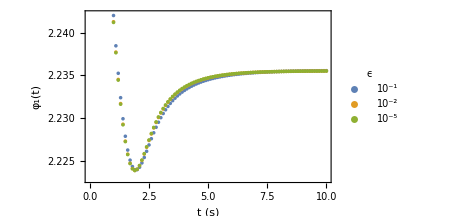
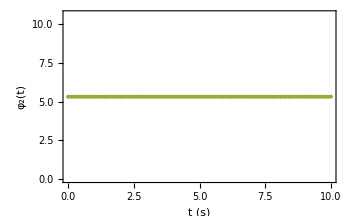
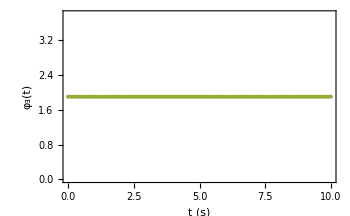
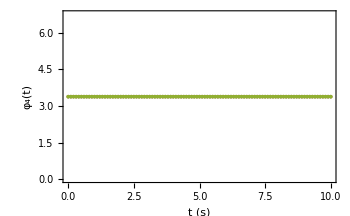
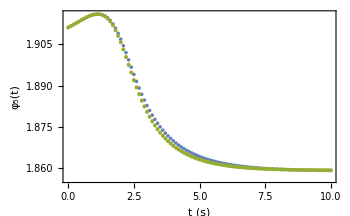
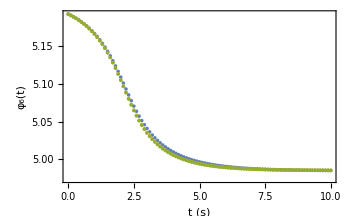
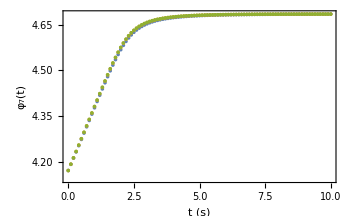
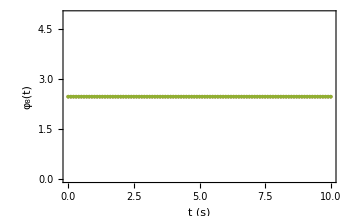
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Grid[{{ListPlot[{φ2List1,φ3List1,φList1},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_1(t)"},PlotLegends->LineLegend[{"10^-1","10^-2","10^-5"},LegendLabel->"ϵ"]],ListPlot[{φ2List2,φ3List2,φList2},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_2(t)"}],ListPlot[{φ3List3,φ3List3,φList3},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_3(t)"}],ListPlot[{φ2List4,φ3List4,φList4},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_4(t)"}],ListPlot[{φ2List5,φ3List5,φList5},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_5(t)"}]},{ListPlot[{φ2List6,φ3List6,φList6},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_6(t)"}],ListPlot[{φ2List7,φ3List7,φList7},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_7(t)"}],ListPlot[{φ2List8,φ3List8,φList8},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_8(t)"}],ListPlot[{φ2List9,φ3List9,φList9},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_9(t)"}],ListPlot[{φ2List10,φ3List10,φList10},Frame->True,ImageSize->350,FrameStyle->Directive[Black,FontSize->14],FrameLabel->{"t (s)","φ_10(t)"}]}},Spacings->2]
```